```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;
K2meV=1000*8.617332478*10^−5;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesC={"C_4685_760.eV","C_4730_1900.eV","C_4759_2500.eV","C_4801_3200.eV","C_4850_3805.eV"};
filesZr={"Zr_4685_760.eV","Zr_4730_1900.eV","Zr_4759_2500.eV","Zr_4801_3200.eV","Zr_4850_3805.eV"};
(* old uses 2 data points for harmonic approximation:
filesCh={"harm.C_4685_760","harm.C_4730_1900","harm.C_4759_2500","harm.C_4801_3200","harm.C_4850_3805"};
filesZrh={"harm.Zr_4685_760","harm.Zr_4730_1900","harm.Zr_4759_2500","harm.Zr_4801_3200","harm.Zr_4850_3805"};
*)
(*New harmonic is only bases on a single displacement of 0.01 Angstrom for both Zr and C:*)
filesCh={"1.harm.C_4685_760.eV","1.harm.C_4730_1900.eV","1.harm.C_4759_2500.eV","1.harm.C_4801_3200.eV","1.harm.C_4850_3805.eV"};
filesZrh={"1.harm.Zr_4685_760.eV","1.harm.Zr_4730_1900.eV","1.harm.Zr_4759_2500.eV","1.harm.Zr_4801_3200.eV","1.harm.Zr_4850_3805.eV"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,5}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,5}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,5}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,5}];
```

```mathematica
(*meV potential*)
cmeV=ReadList["C_4685_760",{Number,Number}];
cmeVh=ReadList["1.harm.C_4685_760",{Number,Number}];
```

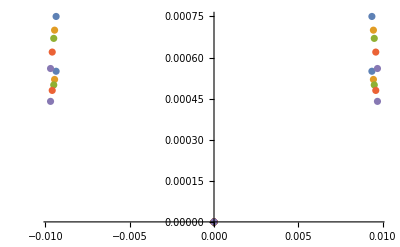

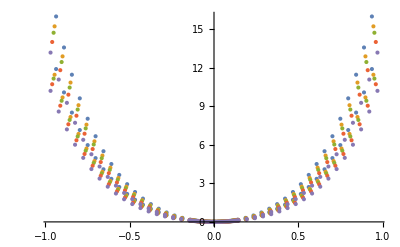

```mathematica
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;

(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,5}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,5}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
```

```mathematica
V[1,4,x][[1]]
VmeV[1,4,x_]:=Fit[cmeV,{x^2,x^4},x];
VmeV[1,2,x_]:=Fit[cmeVh,{x^2},x];
VmeV[1,2,x]
VmeV[1,4,x]
```

5.77479 x^2+8.77582 x^4

6264.46 x^2

5774.79 x^2+8775.82 x^4

```mathematica
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

{6.26446,5.8106,5.52852,5.20833,4.67637}

{1.02135,0.983652,0.959479,0.93128,0.882441}

{8.54244,7.82196,7.40822,6.72743,5.95175}

{0.432764,0.414112,0.403011,0.384048,0.361229}

```mathematica
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]

eKin[dim_]:=(1/(2))* SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
spectrum[n_,tolerance_: .00001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},FixedPoint[{#[[1]]+1,Eigenvalues[h=eKin[#[[1]]]+N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
```

```mathematica
m[[1]]
```

12.0107

```mathematica
s=NDEigensystem[-(1/(2m[[1]]))*u''[x]+(6*x^2+6*x^4)*u[x],u[x],{x,-4,4},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{1.15776,{{0.52749,1.63052,2.82081},{InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x]}}}

```mathematica
s[[1]]
s[[1]]/(2*s[[1]][[1]])
```

{0.707107,2.12132,3.53553}

{0.5,1.5,2.5}

```mathematica
t=spectrum[3][(6*x*x ),x]//Timing
```

{1.42466,{{0.499777,1.49933,2.49888},{ψe[«123»],ψe[«123»],ψe[«123»]}}}

```mathematica
t[[1]]
t[[1]]/(2*t[[1]][[1]])
```

{0.707107,2.12132,3.53553,4.94975,6.36396}

{0.5,1.5,2.5,3.5,4.5}

```mathematica
h={6*x^2+6*x^4};
rule={u_*x^2+v_*x^4}->{(u/m[[1]])*x^2+(v/m[[1]])*(1/m[[1]])^(1/2)*x^4};
hnew=h/.rule
hnew[[1]]
```

{0.499555 x^2+0.144145 x^4}

0.499555 x^2+0.144145 x^4

```mathematica
NDEigensystem[-(1/(2*m[[1]]))*u''[x]+h[[1]]*u[x],u[x],{x,-1.5,1.5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{0.457,{{0.52749,1.63052,2.82081},{InterpolatingFunction[{{-1.5, 1.5}}, <>][x],InterpolatingFunction[{{-1.5, 1.5}}, <>][x],InterpolatingFunction[{{-1.5, 1.5}}, <>][x]}}}

```mathematica
s=NDEigensystem[-(1/(2))*u''[x]+hnew[[1]]*u[x],u[x],{x,-4,4},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{1.2079,{{0.579315,1.85517,3.3289},{InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x]}}}

```mathematica
t=spectrum[3][hnew[[1]],x]//Timing
```

{0.131148,{{0.81964,2.62478,4.70988},{ψe[«21»],ψe[«21»],ψe[«21»]}}}

### Test if can divide through by mass in anharmonic Hamiltonians as well as harmonic

```mathematica
1)Harmonic normal
```

```mathematica
NDEigensystem[-(1/(2*12))*u''[x]+6*(x^2)*u[x],u[x],{x,-4,4},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{1.21302,{{0.5,1.5,2.5},{InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x]}}}

```mathematica
1)Harmonic dimensionless i
```

```mathematica
NDEigensystem[-(1/(2))*u''[x]+0.5(x^2)*u[x],u[x],{x,-5,5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{1.46431,{{0.5,1.5,2.5},{InterpolatingFunction[{{-5., 5.}}, <>][x],InterpolatingFunction[{{-5., 5.}}, <>][x],InterpolatingFunction[{{-5., 5.}}, <>][x]}}}

```mathematica
1)Harmonic dimensionless ii
```

```mathematica
NDEigensystem[-(1)*u''[x]+0.25*(x^2)*u[x],u[x],{x,-8,8},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{2.6331,{{0.5,1.5,2.5},{InterpolatingFunction[{{-8., 8.}}, <>][x],InterpolatingFunction[{{-8., 8.}}, <>][x],InterpolatingFunction[{{-8., 8.}}, <>][x]}}}

```mathematica
1)Quartic normal
Check why quartic Hamiltonian doesn't have at least the first same eigenvalue harmonic?
```

```mathematica
NDEigensystem[-(1/(2*12))*u''[x]+6*(x^2+x^4)*u[x],u[x],{x,-2,2},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{0.614786,{{0.527736,1.6313,2.82219},{InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x]}}}

```mathematica
r1=NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(5.774790695038131 x^2+8.77581901102392 x^4)*u[x],u[x],{x,-4,4},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{0.530329,1.65703,2.90066},{InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x]}}

```mathematica
r1[[1]]/(2r1[[1]][[1]])
```

{0.5,1.56227,2.73477}

```mathematica
r2=NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(6256.4701277595495 x^2+6879.8771523894475 x^4)*u[x],u[x],{x,-1,1},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{16.1728,48.5861,81.1344},{InterpolatingFunction[{{-1., 1.}}, <>][x],InterpolatingFunction[{{-1., 1.}}, <>][x],InterpolatingFunction[{{-1., 1.}}, <>][x]}}

```mathematica
r2[[1]]/(2r2[[1]][[1]])
```

{0.5,1.5021,2.50837}

### Test if eV and meV potentials give the same answers

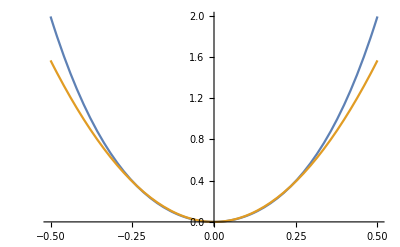

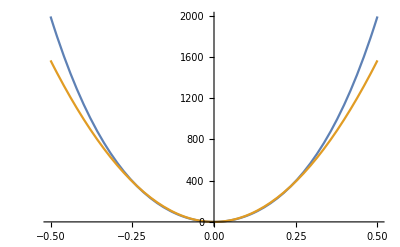

```mathematica
Plot[{Evaluate@V[1,4,x][[1]],Evaluate@V[1,2,x][[1]]},{x,-0.5,0.5}]
Plot[{Evaluate@VmeV[1,4,x],Evaluate@VmeV[1,2,x]},{x,-0.5,0.5}]
```

```mathematica
NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(VmeV[1,2,x])*u[x],u[x],{x,-0.5,0.5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{16.1489,48.4467,80.7444},{InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x]}}

```mathematica
lhmeV=NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(VmeV[1,4,x])*u[x],u[x],{x,-0.5,0.5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{15.552,46.7493,78.1317},{InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x]}}

```mathematica
V[1,4,x][[1]]
```

5.77479 x^2+8.77582 x^4

```mathematica
lheV=NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(V[1,4,x][[1]])*u[x],u[x],{x,-2,2},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{0.530329,1.65703,2.90066},{InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x]}}

```mathematica
lheV[[1]]*Sqrt[1000]
lhmeV[[1]]
```

{16.7705,52.4,91.7269}

{15.552,46.7493,78.1317}

```mathematica
lheV[[1]]/(2*lheV[[1]][[1]])
lhmeV[[1]]/(2*lhmeV[[1]][[1]])
```

{0.5,1.56227,2.73477}

{0.5,1.503,2.51195}

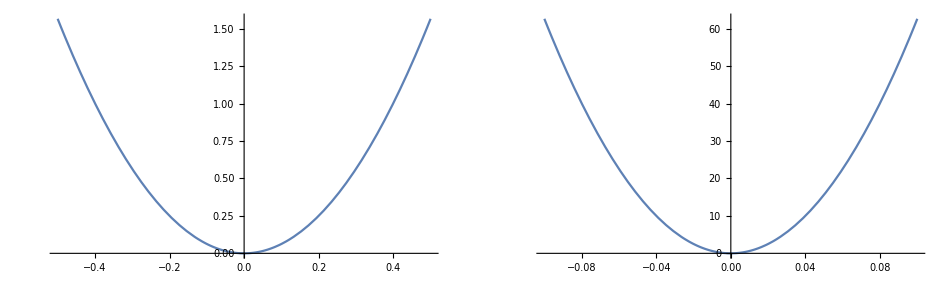

```mathematica
GraphicsGrid[{{Plot[Evaluate@V[1,2,x][[1]],{x,-0.5,0.5}],Plot[Evaluate@VmeV[1,2,x],{x,-0.1,0.1}]}}]
```

```mathematica
VmeV[1,2,x]
V[1,2,x][[1]]
```

6264.46 x^2

6.26446 x^2

```mathematica
Sqrt[2*VmeV[1,2,x][[1]]/m[[1]]]
Sqrt[2*V[1,2,x][[1]][[1]]/m[[1]]]*Sqrt[1000]
```

32.2978

32.2978

### Harmonic non-dimensional

```mathematica
NDEigensystem[-(1/(2*m[[1]]))*u''[x]+(VmeV[1,2,x])*u[x],u[x],{x,-0.5,0.5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{16.1489,48.4467,80.7444},{InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x]}}

```mathematica
NDEigensystem[-(1/(2))*u''[x]+(VmeV[1,2,x]/m[[1]])*u[x],u[x],{x,-0.5,0.5},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{16.1139,47.9349,77.7235},{InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x],InterpolatingFunction[{{-0.5, 0.5}}, <>][x]}}

## Non-dimensional anharmonic

```mathematica
NDEigensystem[-(1/(2*12))*u''[x]+(6x^2+6x^4)*u[x],u[x],{x,-2,2},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{0.527736,1.6313,2.82219},{InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x]}}

```mathematica
rule={u_*x^2+v_*x^4}->{(u/mass)*x^2+(v/mass)*(1/mass)^(1/2)*x^4}
mass=12
```

{x^2 u_+x^4 v_}→{(u x^2)/12+(v x^4)/(24 √3)}

12

```mathematica
NDEigensystem[-(1/(2))*u''[x]+12^-0.5*(6x^2+6x^4)*u[x],u[x],{x,-2,2},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{1.16778,3.81946,6.98627},{InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x]}}

```mathematica
newh={6x^2+6x^4}/.rule
```

{x^2/2+x^4/(4 √3)}

```mathematica
newh[[1]]
NDEigensystem[-(1/(2))*u''[x]+(0.5x^2+(0.0897)x^4)*u[x],u[x],{x,-2,2},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

x^2/2+x^4/(4 √3)

{{0.5277,1.56948,2.63935},{InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x],InterpolatingFunction[{{-2., 2.}}, <>][x]}}

```mathematica
VmeV[1,4,x]
V[1,4,x][[1]]
```

5774.79 x^2+8775.82 x^4

5.77479 x^2+8.77582 x^4

```mathematica
NDEigensystem[-(1/(2*m[[1]]))*u''[x]+VmeV[1,2,x]*u[x],u[x],{x,-1,1},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]
```

{{16.1489,48.4467,80.7444},{InterpolatingFunction[{{-1., 1.}}, <>][x],InterpolatingFunction[{{-1., 1.}}, <>][x],InterpolatingFunction[{{-1., 1.}}, <>][x]}}

```mathematica
NDEigensystem[-(1/(2*m[[1]]))*u''[x]+VmeV[1,4,x]*u[x],u[x],{x,-1,1},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}][[1]]//Timing
```

{0.311417,{15.552,46.7493,78.1317}}

{1.60612,1.6662,1.84672,2.08317,2.26921,2.52423,3.01864,3.09271,3.71122,3.65723,4.26883,4.55892,4.98763,5.05169,5.70495,6.09408,6.51351,6.90522,7.26717,7.55218,7.99814,8.16708,8.43531,9.08132,9.58015,9.98777,10.3248,10.742,11.5004,12.2536,12.2931}

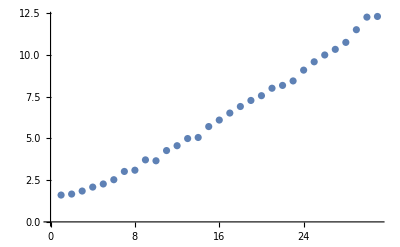

```mathematica
timingdata=Table[Timing[NDEigensystem[-(1)*u''[x]+2*m[[1]]*VmeV[1,4,x]*u[x],u[x],{x,-1,1},i,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}][[1]]/(2*m[[1]])][[1]],{i,50,200,5}]
ListPlot@timingdata
```

```mathematica
NDEigensystem[-(1)*u''[x]+2*m[[1]]*VmeV[1,4,x]*u[x],u[x],{x,-1,1},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}][[1]]/(2m[[1]])//Timing
NDEigensystem[-(1)*u''[x]+2*m[[1]]*VmeV[1,4,x]*u[x],u[x],{x,-1,1},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}][[1]]/(2m[[1]])//Timing
```

{0.391473,{15.552,46.7493,78.1317,109.696,141.44,173.36,205.453,237.718,270.151,302.751}}

{0.361449,{15.552,46.7493,78.1317,109.696,141.44,173.36,205.453,237.718,270.151,302.751}}